```mathematica
states=EntityValue[Entity["Country","UnitedStates"],"AdministrativeDivisions"];
states=Delete[states,{{2},{8},{12},{28}}];

capitals=EntityValue[states,"CapitalCity"];
store = {};
(* all coordiates to a list, this way the geo entities don't have to be used in the calculations as they seemed to be slowing things down?
 *) 

Do [
AppendTo[store,CityData[capitals[[j]],"Coordinates"]];
,{j,Length[capitals]}];


generateMutation[list_]:=
Module[{mutationChance,mutation,mutationChoice,switch,g,v,lowMutationChance,mutationNumber,nList,dupes,dupesOne},
(*this is the mutation function , determines the odds of the mutation occuring and then determines which to choose *) 
nList = list;
mutationNumber = RandomVariate[PoissonDistribution[1]];


Do[
switch = .5;
mutationChoice = RandomReal[{0,1}];
If[mutationChoice < switch,
nList = heuristicMutate[list];
,
nList = insertMutate[list];
];
(*Return[heuristicMutate[list]];*)
,{i,1,mutationNumber}];

Return[nList];

];


insertMutate[list_]:=
Module[{mutationValue,copyList,insertIndex, valueToInsert,destination},
(* mutate function which takes a random coordinate in path and moves it somewhere else *) 

destination = list[[1]];
copyList = list[[2;;Length[list]-1]];

mutationValue = RandomInteger[{1,Length[copyList]}];
insertIndex = RandomInteger[{1,Length[copyList]}];

valueToInsert = copyList[[insertIndex]];

copyList = Delete[copyList,insertIndex];
copyList = Insert[copyList, valueToInsert, mutationValue];

AppendTo[copyList,destination];
PrependTo[copyList,destination];

Return[copyList];


];



triggerSwap[swaps_,originalSwap_,emptySet_]:=
Module[{mutatedSet,replaceIndex,replaceValue,newValue,newIndex,cuq, index},
(* part of the heuristic swap function, chooses 3 places in path and swaps them based on a list of shuffled indexes *) 
mutatedSet =emptySet;
Do[

replaceIndex = originalSwap[[g]];
replaceValue = emptySet[[replaceIndex]];
newValue =  Position[emptySet,swaps[[g]]][[1]][[1]];
newIndex = Position[emptySet,swaps[[g]]];
cuq = originalSwap[[g]];
mutatedSet[[cuq ]]= emptySet[[index]];
mutatedSet[[originalSwap[[g]]]] = emptySet[[swaps[[g]]]];
,{g,Length[swaps]}
];

Return[mutatedSet];
];


heuristicMutate[list_]:= 
Module[{emptySet,destination,backIndex,cOne,cTwo,cThree,pool,fitnesses,potentialPool,minPosition,newList,endingResult,tuples, swapValues},
(*heuristic mutation which chooses three places in a list to swap and then checks all possible combinations in terms of fitness, then returns the best *) 

destination = list[[1]];
emptySet = list[[2;;Length[list]-1]];
swapValues = Sort[RandomSample[Range[Length[emptySet]],3]];
pool = List[];
tuples = Tuples[swapValues,3];

Do[
If[DuplicateFreeQ[tuples[[v]]],
newList = triggerSwap[tuples[[v]],swapValues,emptySet];
AppendTo[pool,newList];
];
,{v,Length[tuples]}
];

potentialPool = {};
potentialPool = pool[[1;;Length[pool]]];
fitnesses = Map[calculateFitness,potentialPool];
minPosition = Position[fitnesses,Min[fitnesses]][[1]][[1]];
endingResult = potentialPool[[minPosition]];

AppendTo[endingResult,destination];
PrependTo[endingResult,destination];
Return[endingResult];

];



swapMutate[list_]:=
Module[{index,newList},
newList=list;
index=RandomInteger[{2,Length[newList]-2}];
newList[[{index,index+1}]]=newList[[{index+1,index}]];
newList
];


getFitnessList[pool_]:=
Module[{fitValue,fitnessList},
fitnessList = List[];
Do[
fitValue = calculateFitness[pool[[i]]];
AppendTo[fitnessList,fitValue];
,{i,Length[pool]}];

Return[fitnessList];
];


crossOver[listOne_,listTwo_]:=
Module[{topChunk,bottomChunk,start,end,emptySet,currentBottomPiece,currentTopPiece,replaceValueIndex},
(* PMX crossover function, gets chunk from list one and then attempts to place all parts of listTwo as accurate as possbile based on ther positions in listOne *)

end = RandomInteger[{3,Length[listOne]}];
start = RandomInteger[{1,end-1}];
topChunk = listOne[[start;;end]];

bottomChunk = listTwo[[start;;end]];
emptySet = Table[x,{Length[listOne]}];
emptySet[[start;;end]] = topChunk;

Do[

currentBottomPiece = bottomChunk[[i]];
currentTopPiece = topChunk[[i]];
If[currentBottomPiece ≠ currentTopPiece && !MemberQ[topChunk,currentBottomPiece],
replaceValueIndex = Position[listTwo,search[listOne,listTwo,bottomChunk[[i]],bottomChunk]][[1]][[1]];
emptySet[[replaceValueIndex]] = bottomChunk[[i]];
];
,{i,Length[bottomChunk]}];

Do[

If[emptySet[[i]] == x,
emptySet[[i]] = listTwo[[i]];
];

,{i,Length[emptySet]}];

Return[emptySet];
];


(*recursive function part of PMX *) 
search[listOne_,listTwo_,value_,chunk_]:=
Module[{listOneValue},
indexValue = Position[listTwo,value][[1]][[1]];
listOneValue = listOne[[indexValue]];
If[MemberQ[chunk,listOneValue],
Return[search[listOne,listTwo,listOneValue,chunk]];
,
Return[listOneValue];
];

];



createPaths[list_,start_,numberOfPaths_]:= 
Module[{nList,end,totalSet},
(*creates a random set of paths with a designated start and end *) 

totalSet = List[];
Do [
end = start;
nList = List[];
positionStart = Position[list,start];
sample = Delete[list,positionStart];
positionEnd = Position[sample,end];
sample = Delete[sample,positionEnd];
nList =RandomSample[sample,Length[sample]];
PrependTo[nList,start];
AppendTo[nList,start];
totalSet = Append[totalSet,nList];
,{i,numberOfPaths}];
Return[totalSet];
]


calculateFitness[list_]:=
Module[{sum},
(*calculates fitness from a path*) 
sum = 0;
Do[
sum = sum + EuclideanDistance[list[[i]],list[[i+1]]];
,{i,Length[list]-1}];
Return[N[sum]];
]


calculateTotalFitness[lists_]:=
(* this calculates fitness for total pool, usefull for measuring convergence *) 
Module[{sum},
sum = 0;
Do[
sum = sum + calculateFitness[lists[[i]]];
,{i,Length[lists]}];
Return[N[sum]];
];


graphTotal[lists_]:=
(*graph function which can used to show paths and fitnesses in a pool *) 
Module[{sum},
sum = 0;
Do[
Print[N[Graphics[Line[lists[[i]]]]]];
Print[N[calculateFitness[lists[[i]]]]];
,{i,Length[lists]}]

];




elitism[paths_]:=
Module[{},
(* finds the fitest path in a pool *) 
a = Map[calculateFitness,paths];
index = Position[a,Min[a]][[1]][[1]];
Return[paths[[index]]];
];



tournamentSmall[paths_]:=
Module[{choiceOne,choiceTwo, choiceOneFitness,choiceTwoFitness,choiceOneCrossFitness,choiceTwoCrossFitness,choiceOneCrossOver,choiceTwoCrossOver,pool,coordinateValues,coordinateFitness,minVal,coordinate,poolLength},
pool = List[];

Do[

(* tournament selection algo takes two random choices and compares them *) 
choiceOne = RandomChoice[paths];
choiceTwo = RandomChoice[paths];
choiceOneFitness = calculateFitness[choiceOne];
choiceTwoFitness = calculateFitness[choiceTwo];

If[choiceOneFitness < choiceTwoFitness,
AppendTo[pool,generateMutation[choiceOne]];
,
AppendTo[pool,generateMutation[choiceTwo]];
];

,{k,Length[paths]}];


Return[pool];
];


runCrossOver[paths_]:=
Module[{choicene,choicewo,newPool,newCross},

newPool = List[];

Do[

mutationChance =.2; 
mutation = RandomReal[{0,1}];

If[mutation < mutationChance,
choicene = RandomChoice[paths];
choicewo = RandomChoice[paths];
newCross = crossOver[choicene,choicewo];
AppendTo[newPool,newCross];
,
AppendTo[newPool,paths[[b]]];
];

,{b,Length[paths]}];

Return[newPool];
];




ordering[listOne_,listTwo_]:=
Module[{position,genOrder,cleanPos},
genOrder = {}; 

Do[
position = Position[listOne,listTwo[[x]]]; 
cleanPos = position[[1]][[1]];
AppendTo[genOrder,cleanPos];
,{x,Length[listOne]}];

AppendTo[genOrder,1];
Return[genOrder];
];
```

{}

```mathematica
nPaths= 100;
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression index$501937 cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pkspec1: The expression index$503644 cannot be used as a part specification.

Part::pkspec1: The expression index$504154 cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

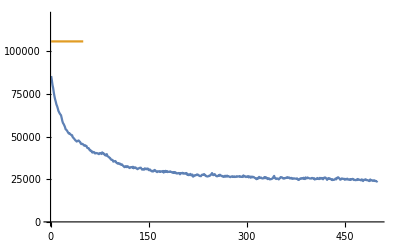

-Graphics-

```mathematica
mathematicaOp = FindShortestTour[store];
per = N[calculateFitness[mathematicaOp]]*nPaths;
randompaths = createPaths[store,{32.3462512,-86.2685927},nPaths];


Do[
population = randompaths;
g = List[];

Do[
population = runCrossOver[tournamentSmall[population]];
AppendTo[g,calculateTotalFitness[population]];
,{i,500}];


Print[ListLinePlot[{g,Table[per,{50}]},PlotRange->{0,120500}]];
,{u,1}];

GeoListPlot[capitals[[ordering[store,population[[1]]]]],Joined->True,ImageSize->{800,400}]

(* currently algoritm is set to run 500 times, with nPaths being the number of paths generated, i is the number of times it runs, and u is how many times the entire thing repeats,

there are some weight list outputs but it converges pretty well, right now a graph is printed of aggregate fitness in pool overtime, and a final path from the pool in its last state is printed on the map

with these parameters the algorithm takes  about 30 seconds 

 *)
```